# P5 with NFW potential

## Q1 (0.85-0.880)

### q1 = 0.85

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch8cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test8.csv",{"Data",2,1;;2}];
ch8clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test8.csv",{"Data",2,3;;4}];
ch8lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test8.csv",{"Data",3;;6001,1;;2}];
ch8tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test8.csv",{"Data",3;;6001,5;;6}];
```

Graph

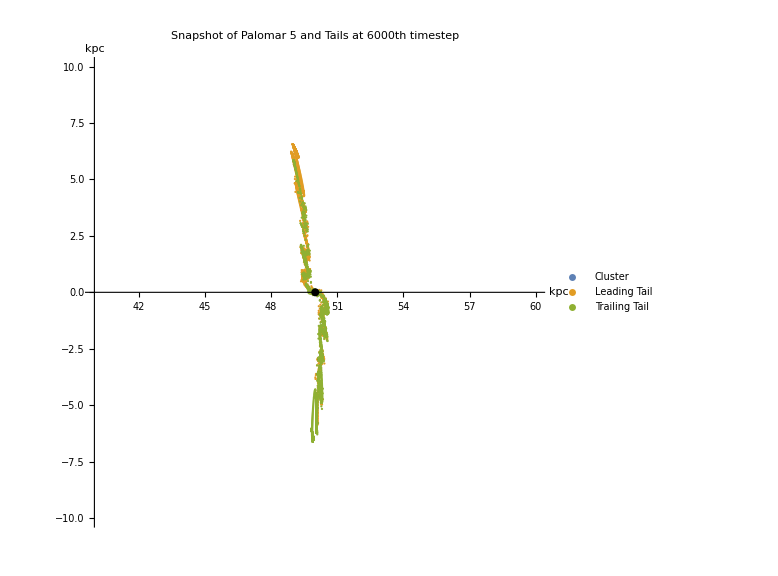

```mathematica
ch8orbit =  ListPlot[{ch8cl,ch8lt,ch8tt},ImageSize->Large,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch8cl}]},PlotLegends->{"Cluster","Leading Tail","Trailing Tail"},PlotRange->{{40,60},{-10,10}}, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### q1 = 0.86

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch9cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test9.csv",{"Data",2,1;;2}];
ch9clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test9.csv",{"Data",2,3;;4}];
ch9lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test9.csv",{"Data",3;;6001,1;;2}];
ch9tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test9.csv",{"Data",3;;6001,5;;6}];
```

Graph

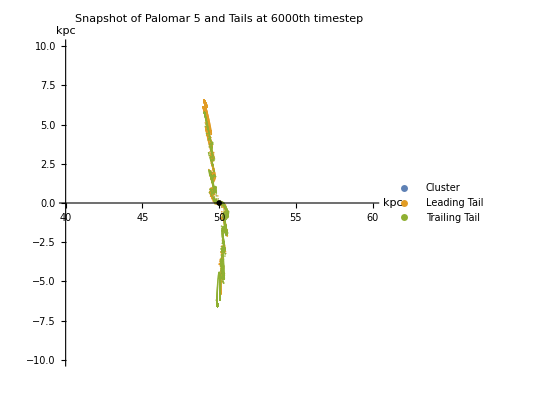

```mathematica
ch9orbit =  ListPlot[{ch9cl,ch9lt,ch9tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch9cl}]},PlotLegends->{"Cluster","Leading Tail","Trailing Tail"},PlotRange->{{40,60},{-10,10}}, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### q1=0.87

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch10cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test10.csv",{"Data",2,1;;2}];
ch10clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test10.csv",{"Data",2,3;;4}];
ch10lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test10.csv",{"Data",3;;6001,1;;2}];
ch10tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test10.csv",{"Data",3;;6001,5;;6}];
```

Graph

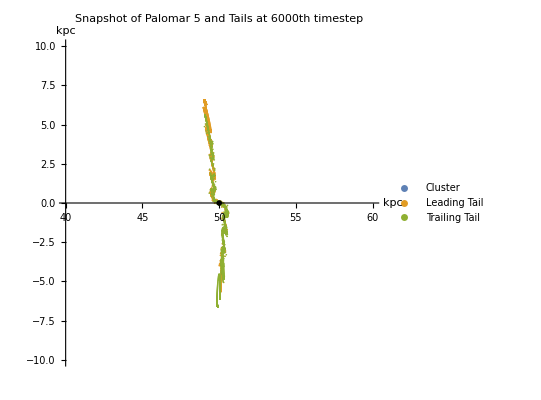

```mathematica
ch10orbit =  ListPlot[{ch10cl,ch10lt,ch10tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch10cl}]},PlotLegends->{"Cluster","Leading Tail","Trailing Tail"},PlotRange->{{40,60},{-10,10}}, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### q1=0.88

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch11cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test11.csv",{"Data",2,1;;2}];
ch11clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test11.csv",{"Data",2,3;;4}];
ch11lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test11.csv",{"Data",3;;6001,1;;2}];
ch11tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test11.csv",{"Data",3;;6001,5;;6}];
```

Graph

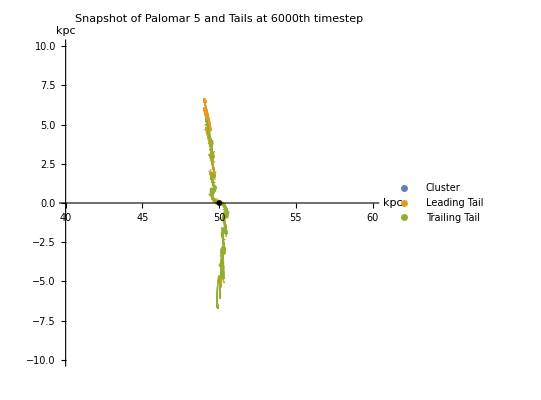

```mathematica
ch11orbit =  ListPlot[{ch11cl,ch11lt,ch11tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch11cl}]},PlotLegends->{"Cluster","Leading Tail","Trailing Tail"},PlotRange->{{40,60},{-10,10}}, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### Comparing q1

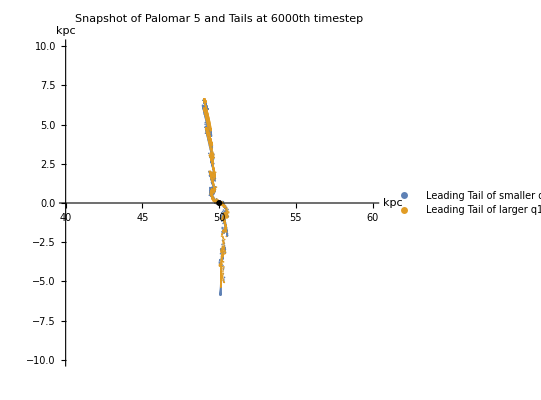

```mathematica
compq1orbit =  ListPlot[{ch8lt,ch11lt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch8cl,ch11cl}]},PlotLegends->{"Leading Tail of smaller q1 ","Leading Tail of larger q1"},PlotRange->{{40,60},{-10,10}}, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

## Initial Position (15-150 kpc at apocenter)

### initial position = 15 kpc

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Velocity of Cluster = 0.5 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q1=q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch12cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test12.csv",{"Data",2,1;;2}];
ch12clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test12.csv",{"Data",2,3;;4}];
ch12lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test12.csv",{"Data",3;;6001,1;;2}];
ch12tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test12.csv",{"Data",3;;6001,5;;6}];
```

Graph

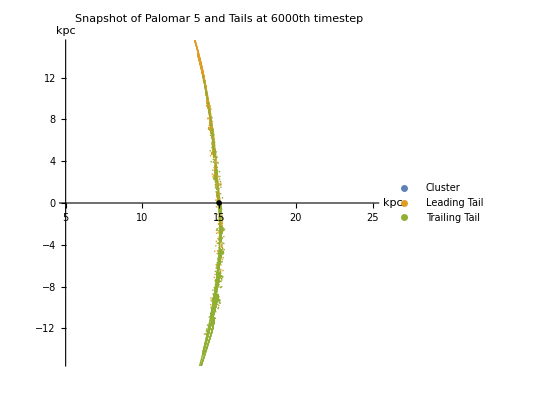

```mathematica
ch12orbit =  ListPlot[{ch12cl,ch12lt,ch12tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch12cl}]},PlotLegends->{"Cluster","Leading Tail","Trailing Tail"},PlotRange->{{5,25},{-15,15}}, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### initial position = 50 kpc

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Velocity of Cluster = 0.5 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q1=q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch13cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test13.csv",{"Data",2,1;;2}];
ch13clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test13.csv",{"Data",2,3;;4}];
ch13lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test13.csv",{"Data",3;;6001,1;;2}];
ch13tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test13.csv",{"Data",3;;6001,5;;6}];
```

Graph

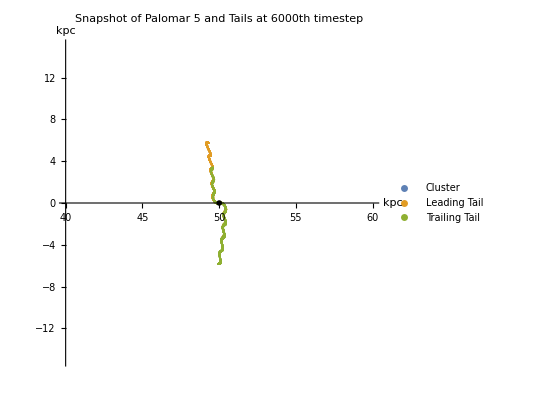

```mathematica
ch13orbit =  ListPlot[{ch13cl,ch13lt,ch13tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch13cl}]},PlotLegends->{"Cluster","Leading Tail","Trailing Tail"},PlotRange->{{40,60},{-15,15}}, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### Initial position = 100 kpc

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Velocity of Cluster = 0.5 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q1=q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch14cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test14.csv",{"Data",2,1;;2}];
ch14clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test14.csv",{"Data",2,3;;4}];
ch14lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test14.csv",{"Data",3;;6001,1;;2}];
ch14tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test14.csv",{"Data",3;;6001,5;;6}];
```

Graph

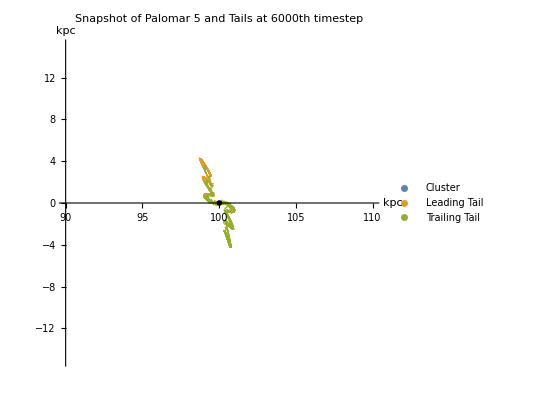

```mathematica
ch14orbit =  ListPlot[{ch14cl,ch14lt,ch14tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch14cl}]},PlotLegends->{"Cluster","Leading Tail","Trailing Tail"},PlotRange->{{90,110},{-15,15}}, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### Initial position = 150 kpc

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Velocity of Cluster = 0.5 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q1=q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch15cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test15.csv",{"Data",2,1;;2}];
ch15clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test15.csv",{"Data",2,3;;4}];
ch15lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test15.csv",{"Data",3;;6001,1;;2}];
ch15tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test15.csv",{"Data",3;;6001,5;;6}];
```

Graph

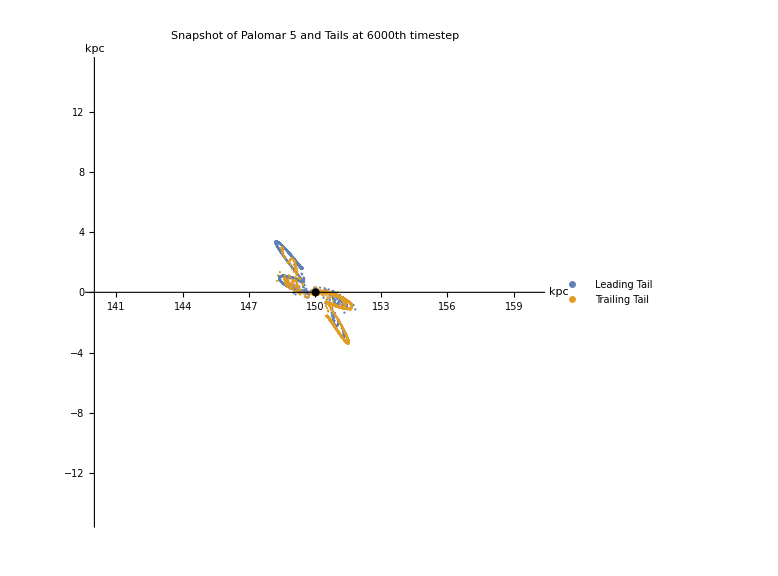

```mathematica
ch15orbit =  ListPlot[{ch15lt,ch15tt},ImageSize->Large,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch15cl}]},PlotLegends->{"Leading Tail","Trailing Tail"},PlotRange->{{140,160},{-15,15}}, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### Comparing initial positions

Graph

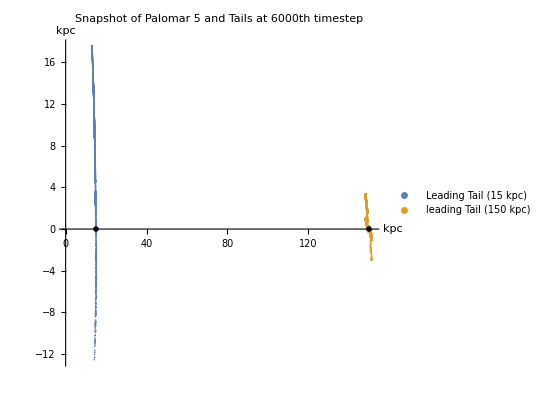

```mathematica
compinitposorbit = ListPlot[{ch12lt,ch15lt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch15cl,ch12cl}]},PlotLegends->{"Leading Tail (15 kpc)","leading Tail (150 kpc)"}, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

## Initial Velocity (0.25-1 Vc)

### initial velocity = 0.25 Vc

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.25 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q1=q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch16cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test16.csv",{"Data",2,1;;2}];
ch16clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test16.csv",{"Data",2,3;;4}];
ch16lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test16.csv",{"Data",3;;6001,1;;2}];
ch16tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test16.csv",{"Data",3;;6001,5;;6}];
```

Graph

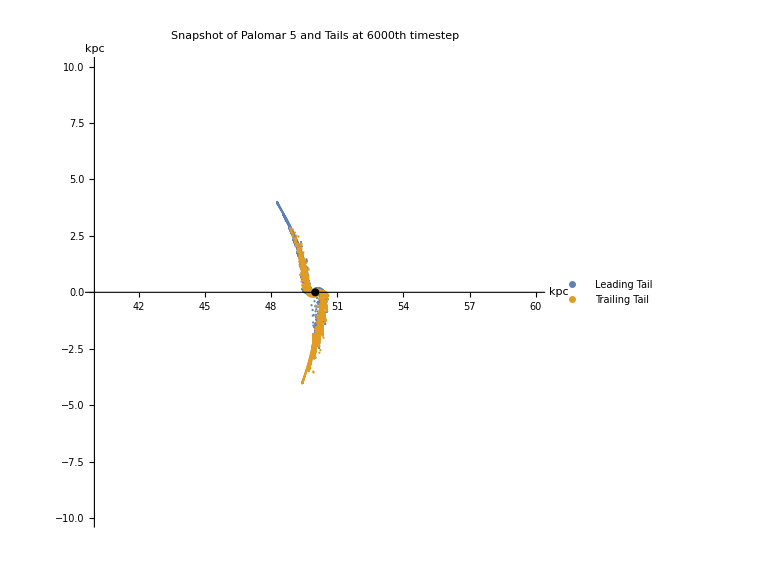

```mathematica
ch16orbit =  ListPlot[{ch16lt,ch16tt},ImageSize->Large,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch16cl}]},PlotRange->{{40,60},{-10,10}},PlotLegends->{"Leading Tail","Trailing Tail"},PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### initial velocity = 0.5 Vc

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.25 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q1=q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch17cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test17.csv",{"Data",2,1;;2}];
ch17clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test17.csv",{"Data",2,3;;4}];
ch17lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test17.csv",{"Data",3;;6001,1;;2}];
ch17tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test17.csv",{"Data",3;;6001,5;;6}];
```

Graph

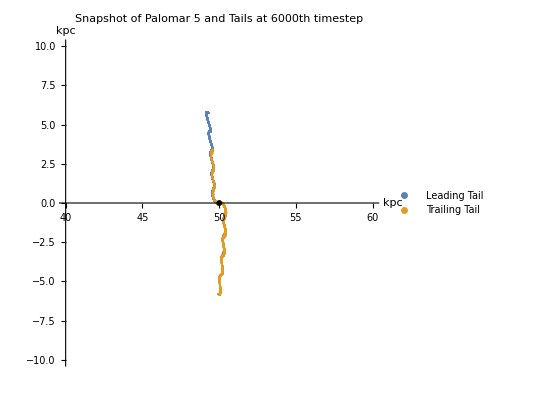

```mathematica
ch17orbit =  ListPlot[{ch17lt,ch17tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch17cl}]},PlotRange->{{40,60},{-10,10}},PlotLegends->{"Leading Tail","Trailing Tail"},PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### initial velocity = 0.75 Vc

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.25 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q1=q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch18cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test18.csv",{"Data",2,1;;2}];
ch18clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test18.csv",{"Data",2,3;;4}];
ch18lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test18.csv",{"Data",3;;6001,1;;2}];
ch18tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test18.csv",{"Data",3;;6001,5;;6}];
```

Graph

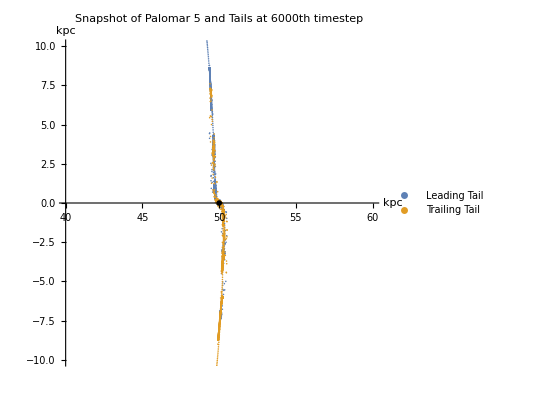

```mathematica
ch18orbit =  ListPlot[{ch18lt,ch18tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch18cl}]},PlotRange->{{40,60},{-10,10}},PlotLegends->{"Leading Tail","Trailing Tail"},PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### Initial Velocity = 1.0 Vc

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.25 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q1=q2=1 qz = 0.94 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch19cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test19.csv",{"Data",2,1;;2}];
ch19clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test19.csv",{"Data",2,3;;4}];
ch19lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test19.csv",{"Data",3;;6001,1;;2}];
ch19tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test19.csv",{"Data",3;;6001,5;;6}];
```

Graph

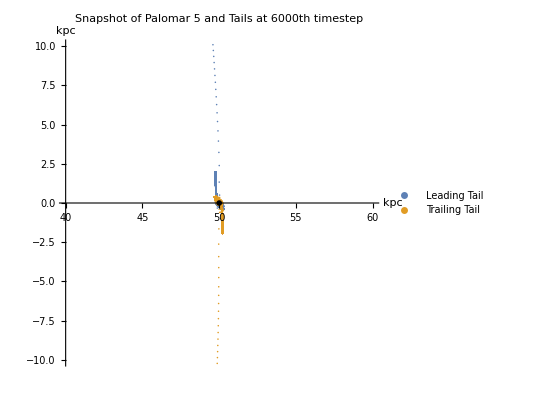

```mathematica
ch19orbit =  ListPlot[{ch19lt,ch19tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch18cl}]},PlotRange->{{40,60},{-10,10}},PlotLegends->{"Leading Tail","Trailing Tail"},PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

### Comparing initial velocity

Graph

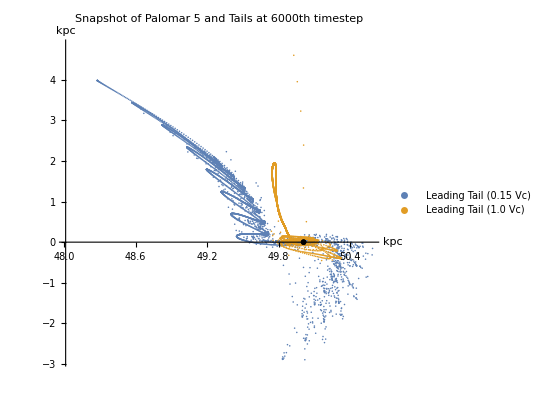

```mathematica
compinitvelorbit = ListPlot[{ch16lt,ch19lt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch16cl,ch19cl}]},PlotLegends->{"Leading Tail (0.15 Vc) ","Leading Tail (1.0 Vc)"}, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

## Recreating figure 3

### Version 1

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 125 kpc,0,0 Initial Velocity of Cluster = 1.0 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU GM = based on vh and rh Msun Vh = 417 km/s Rh = 36.54 kpc phi = 90 degrees q1=0.855 q2=1 qz = 1.2 snapshot at 6000th timestep

Import Coordinates

```mathematica
ch20cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test20.csv",{"Data",2,1;;2}];
ch20clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test20.csv",{"Data",2,3;;4}];
ch20lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test20.csv",{"Data",3;;6001,1;;2}];
ch20tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/P5-NFW/test20.csv",{"Data",3;;6001,5;;6}];
```

Graph

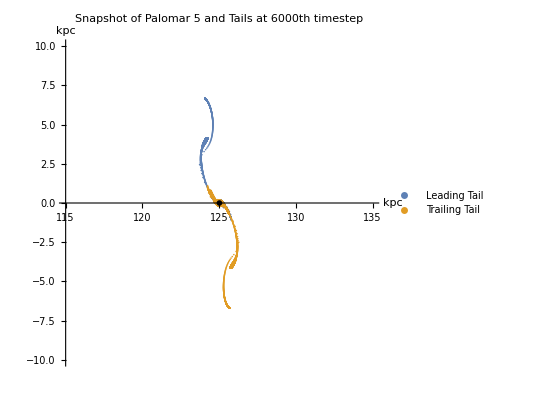

```mathematica
ch20orbit =  ListPlot[{ch20lt,ch20tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch20cl}]},PlotRange->{{115,135},{-10,10}},PlotLegends->{"Leading Tail","Trailing Tail"},PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```